Case 1: Ω_M=0.3, Ω_Λ=0.7 for ΛCDM model.

```mathematica
Integrate[( x (3/10  x^-3 + 7/10 )^(1/2))^-3,{x,0,a}]
( x (3/10  x^-3 + 7/10 )^(1/2))^-3
```

-1/(9 (3+7 a^3))4 √(10/3) a √(a^3) (-24 Hypergeometric2F1[-1/2,5/6,11/6,-(7 a^3)/3]+(15+14 a^3) Hypergeometric2F1[1/2,5/6,11/6,-(7 a^3)/3])

The growth function for this special case of ΛCDM model.

```mathematica
f[a_]=5/2 3/10 (3/10 a^-3 +7/10)^(1/2)  ( -1/(9 (3+7 a^3))4 √(10/3) a √(a^3) (-24 Hypergeometric2F1[-1/2,5/6,11/6,-(7 a^3)/3]+(15+14 a^3) Hypergeometric2F1[1/2,5/6,11/6,-(7 a^3)/3]))
```

-1/(3 (3+7 a^3))√(10/3) √(7/10+3/(10 a^3)) a √(a^3) (-24 Hypergeometric2F1[-1/2,5/6,11/6,-(7 a^3)/3]+(15+14 a^3) Hypergeometric2F1[1/2,5/6,11/6,-(7 a^3)/3])

Compare the ΛCMD and sCDM.

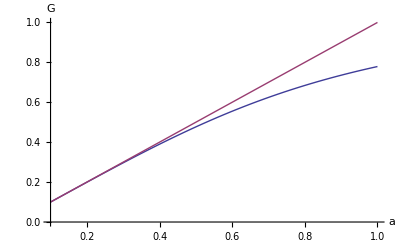

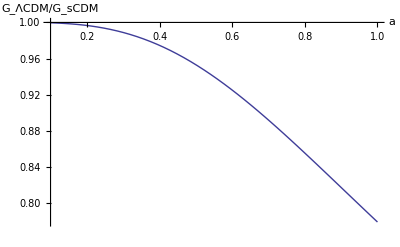

```mathematica
Plot[{f[a],a},{a,0.1,1},AxesLabel-> {a,G},AxesOrigin->{0.1,0}]
Plot[f[a]/a,{a,0.1,1},AxesLabel->{a,Subscript[G, ΛCDM]/Subscript[G, sCDM]},AxesOrigin->{0.1,1}]
```

Case2: Ω_M=n, Ω_Λ=1-n for ΛCDM model.

```mathematica
Integrate[( x ( n  x^-3 + 1-n )^(1/2))^-3,{x,0,a}]
```

ConditionalExpression[-(2 a √(-(a^3 (-1+n))/n) (8 n Hypergeometric2F1[-1/2,5/6,11/6,(a^3 (-1+n))/n]+(2 a^3 (-1+n)-5 n) Hypergeometric2F1[1/2,5/6,11/6,(a^3 (-1+n))/n]))/(15 √(1-n) (a^3 (-1+n)-n) n),Re[n]<1]

The growth function for this general case.

```mathematica
g[a_]=-(2 a √(-(a^3 (-1+n))/n) (8 n Hypergeometric2F1[-1/2,5/6,11/6,(a^3 (-1+n))/n]+(2 a^3 (-1+n)-5 n) Hypergeometric2F1[1/2,5/6,11/6,(a^3 (-1+n))/n]))/(15 √(1-n) (a^3 (-1+n)-n) n) 5/2 n ( n  a^-3 + 1-n)^(1/2)
```

-(a √(-(a^3 (-1+n))/n) √(1-n+n/a^3) (8 n Hypergeometric2F1[-1/2,5/6,11/6,(a^3 (-1+n))/n]+(2 a^3 (-1+n)-5 n) Hypergeometric2F1[1/2,5/6,11/6,(a^3 (-1+n))/n]))/(3 √(1-n) (a^3 (-1+n)-n))

Case3: DE models with a EoS w.

(There is something wrong with this general solution. Check this if it is to be used.)

```mathematica
Integrate[( x ( n  x^-3 + (1-n) x^(-3(1+w)) )^(1/2))^-3,{x,0,a}]
```

ConditionalExpression[-(2 a^(1+3 w) Hypergeometric2F1[1,1+5/(6 w),5/6 (3+1/w),(a^(3 w) n)/(-1+n)])/((-1+n) √(a^(-3 (1+w)) (1+(-1+a^(3 w)) n)) (5+9 w)),Re[w]>0]

Examples:   w=-0.9 , n=0.3

```mathematica
n=3/10;
w=(-9/10);
Integrate[( x ( n  x^-3 + (1-n) x^(-3(1+w)) )^(1/2))^-3,{x,0,a}]
5/2 n ( n  a^-3 + (1-n) a^(-3(1+w)) )^(1/2)
```

ConditionalExpression[-1/(81 (3+7 a^(27/10)))4 √(10/3) a^(5/2) (-231 Hypergeometric2F1[-1/2,25/27,52/27,-(7 a^(27/10))/3]+(150+161 a^(27/10)) Hypergeometric2F1[1/2,25/27,52/27,-(7 a^(27/10))/3]),a>0]

3/4 √(3/(10 a^3)+7/(10 a^(3/10)))

```mathematica
g32[a_]=3/4 √(3/(10 a^3)+7/(10 a^(3/10))) (-1/(81 (3+7 a^(27/10)))4 √(10/3) a^(5/2) (-231 Hypergeometric2F1[-1/2,25/27,52/27,-(7 a^(27/10))/3]+(150+161 a^(27/10)) Hypergeometric2F1[1/2,25/27,52/27,-(7 a^(27/10))/3]))
```

-1/(27 (3+7 a^(27/10)))√(10/3) √(3/(10 a^3)+7/(10 a^(3/10))) a^(5/2) (-231 Hypergeometric2F1[-1/2,25/27,52/27,-(7 a^(27/10))/3]+(150+161 a^(27/10)) Hypergeometric2F1[1/2,25/27,52/27,-(7 a^(27/10))/3])

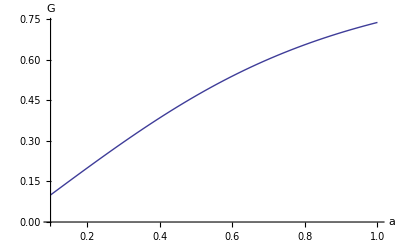

```mathematica
Plot[g32[a],{a,0.1,1},AxesLabel->{a,G},AxesOrigin->{0.1,0}]
```

w=-1.0 , n=0.3

```mathematica
n=3/10;
w=(-1);
Integrate[( x ( n  x^-3 + (1-n) x^(-3(1+w)) )^(1/2))^-3,{x,0,a}]
```

-1/(9 (3+7 a^3))4 √(10/3) a √(a^3) (-24 Hypergeometric2F1[-1/2,5/6,11/6,-(7 a^3)/3]+(15+14 a^3) Hypergeometric2F1[1/2,5/6,11/6,-(7 a^3)/3])

```mathematica
n=3/10;
w=(-1);
g31[a_]=5/2 n ( n  a^-3 + (1-n) a^(-3(1+w)) )^(1/2) (-1/(9 (3+7 a^3))4 √(10/3) a √(a^3) (-24 Hypergeometric2F1[-1/2,5/6,11/6,-(7 a^3)/3]+(15+14 a^3) Hypergeometric2F1[1/2,5/6,11/6,-(7 a^3)/3]))
```

-1/(3 (3+7 a^3))√(10/3) √(7/10+3/(10 a^3)) a √(a^3) (-24 Hypergeometric2F1[-1/2,5/6,11/6,-(7 a^3)/3]+(15+14 a^3) Hypergeometric2F1[1/2,5/6,11/6,-(7 a^3)/3])

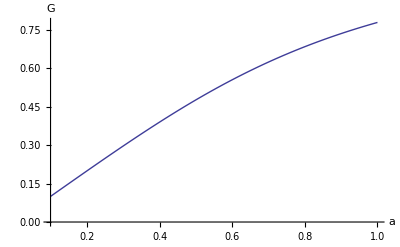

```mathematica
Plot[g31[a],{a,0.1,1},AxesLabel->{a,G},AxesOrigin->{0.1,0}]
```

w=-1.1 , n=0.3

```mathematica
n=3/10;
w=(-1.1);
Integrate[( x ( n  x^-3 + (1-n) x^(-3(1+w)) )^(1/2))^-3,{x,0,a}]
5/2 n ( n  a^-3 + (1-n) a^(-3(1+w)) )^(1/2)
```

ConditionalExpression[2.43432 a^2.5 Hypergeometric2F1[0.757576,1.5,1.75758,-2.33333 a^3.3],a>0]

3/4 √(3/(10 a^3)+(7 a^0.3)/10)

```mathematica
n=3/10;
w=(-1);
g33[a_]=3/4 √(3/(10 a^3)+(7 a^0.30000000000000027)/10)(-1/(9 (3+7 a^3))4 √(10/3) a √(a^3) (-24 Hypergeometric2F1[-1/2,5/6,11/6,-(7 a^3)/3]+(15+14 a^3) Hypergeometric2F1[1/2,5/6,11/6,-(7 a^3)/3]))
```

-1/(3 (3+7 a^3))√(10/3) √(3/(10 a^3)+(7 a^0.3)/10) a √(a^3) (-24 Hypergeometric2F1[-1/2,5/6,11/6,-(7 a^3)/3]+(15+14 a^3) Hypergeometric2F1[1/2,5/6,11/6,-(7 a^3)/3])

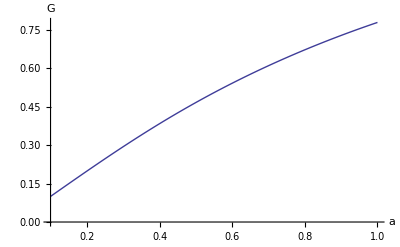

```mathematica
Plot[g33[a],{a,0.1,1},AxesLabel->{a,G},AxesOrigin->{0.1,0}]
```

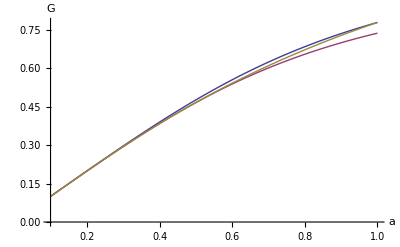

```mathematica
Plot[{g31[a],g32[a],g33[a]},{a,0.1,1},AxesLabel-> {a,G},AxesOrigin->{0.1,0}]
```

Blue is g31. Red is g32. Green is g33.

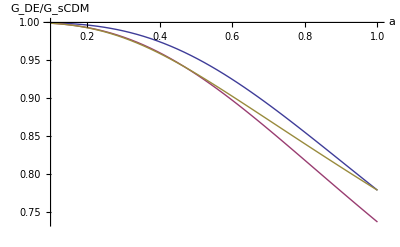

```mathematica
Plot[{g31[a]/a,g32[a]/a,g33[a]/a},{a,0.1,1},AxesLabel-> {a,Subscript[G, DE]/G_sCDM},AxesOrigin->{0.1,1}]
```